# Text Generation using GANs

Suman Sigdel

Bennington College

Generative Adversarial Networks have been used mostly for image data and are known to produce data that closely match the given input eg. deep fakes. Text generation is an area in which GANs are used less given the discrete structures of text. We believe that CNN based GAN architecture used for images can also be used in text generation to generate comparable results to that of RNN models. A comparison between GANs and RNNs will be made to draw a clear distinction between the results they produce using n-gram distributions as a performance metric. 

Application : 
Text generation models can be used for :  product names, naming new chemicals, naming new startups etc.

## Wolfram Community Post (material for blog post)

Introduction
Generative Adversarial Networks or GANs are most commonly known to produce results that are almost indistinguishable from the real dataset eg. Deep Fakes. GANs consist of two neural networks, Generator and Discriminator which compete in an adversarial zero sum game in order to generate plausible examples. The generator never sees the actual training data and only gets data from a latent space, to which it assigns meaning with the help of the discriminator. The discriminator is trained with samples generated by the generator and the samples from the training dataset and learns to classify between real and fake data. The two models operate in a zero sum game in a sense that when the discriminator successfully classifies real and fake samples, it is rewarded with no updates made to the model parameters, however the generator is penalized with large updates. Similarly, when the generator generates plausible examples, only the discriminator’s parameters are updated.
Large amounts of research have been done with GANs for image translation, generation of deep fakes and data augmentation, but GANs application in text and NLP is an area that is less explored.

Aim
In this project, I will be applying GANs for text generation and will be comparing the results with existing Recurrent Neural Networks. This project aims to show that through adversarial training better text generation results can be achieved which is comparable to existing RNN models. This post is divided into 4 sections. In the first section, I will explain the metric that will be used to measure the performance of the text generation models. I will then explain the GAN architecture that was used for text generation and will show it’s performance while generating texts of various domains eg. Chemical Names, Pokemon Names, Company names etc. I will then train existing RNN language model (baseline) with the same datasets and finally will make a comparison between the performance of GAN and existing models.

Performance Metric

Normalizing text

To compare the different model performances, we will be finding the euclidean distance of n-grams between text generated from two models. The initial step will be to remove special characters and diacritics from the real dataset. The following code accomplishes this goal by using a combination of StringReplace, ToLowerCase and Remove Diacritics functions to normalize the characters in the dataset.

```mathematica
normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"->"",(*Remove gender hints*)
	"-"|"-"|"'"->" ",(*Remove very rare characters*)
	DigitCharacter->"" ,(*Remove very rare characters*)
	"("|")" -> "",(*Remove Brackets*)
	"%"|":" -> "",(*Remove Colons and %*)
	"ʻ" |"‘"->  "",(*Remove other special characters*)
	"`"->"",
	" " -> "",
	"="|"?"->"",
	"}"|"{"-> ""}
]
```

Computing n-grams

The next step is to create a lookup table for the different characters so that we can put them in their respective coordinates in the sparse array. The following code makes an association that maps characters and special tokens to an unique point.

```mathematica
characters = AssociationThread[
	Join[CharacterRange["a","z"], {" ", StartOfString, EndOfString}]
	-> Range[29]];
```

A function to compute n-grams is created which computes n-gram for a given wordlist and puts frequencies of each n-gram in a SparseArray. A sparse-array is chosen for faster computation for higher “n” in the n-grams.

```mathematica
computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters],n]]
];
```

Example

Running the following code will normalize chemical names.

```mathematica
chemicalNames = EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[c,StringMatchQ[#,CharacterRange["A","z"]..]&];
tennormalizednames = Take[normalizeText@chemicalNames,10]
```

{hydrogen,helium,deuterium,lithium,beryllium,boron,diamond,graphite,borane,methane}

The following code will then compute the 1 and 2 grams and map their indices to respective normalized occurrences in a SparseArray.

```mathematica
computeNGrams[tennames,1]
computeNGrams[tennames,2]
```

SparseArray[…]

SparseArray[…]

Euclidean Distance between n-gram distributions

We then compute the euclidean distance between the distributions of n-grams in the dataset and generated text. The findEuclideanDistance computes the euclidean distance between two n gram distributions. The DistancesofNgrams function takes the generator and the training dataset to find the euclidean distance between n-gram distributions (between generated and training dataset) where n goes from 1 to 5.

```mathematica
findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2]

DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[100],n], computeNGrams[RandomChoice[dataset,100],n]],{n,1,5}]
```

Using this metric we will be able to compare the GAN model as well as the RNN model. In addition, we will be able to see how the euclidean distance converges as the GAN model is trained.

## ( Murgue T., de la Higuera C. (2004) Distances between Distributions: Comparing Language Models. In: Fred A., Caelli T.M., Duin R.P.W., Campilho A.C., de Ridder D. (eds) Structural, Syntactic, and Statistical Pattern Recognition. SSPR /SPR 2004. Lecture Notes in Computer Science, vol 3138. Springer, Berlin, Heidelberg)

## 2. Baseline RNN Model The baseline RNN model that will be used for comparison is the pretrained "Wolfram English Character-Level Language Model V1". https://resources.wolframcloud.com/NeuralNetRepository/resources/Wolfram-English-Character-Level-Language-Model-V1#:~:text=This%20language%20model%20is%20based,on%20sequences%20of%20length%2080.Nonehttps://resources.wolframcloud.com/NeuralNetRepository/resources/Wolfram-English-Character-Level-Language-Model-V1#:~:text=This%20language%20model%20is%20based,on%20sequences%20of%20length%2080.HyperlinkActionRecycledHyperlinkActiveThe following is the architecture of this model :

```mathematica
NetModel["Wolfram English Character-Level Language Model V1"]
```

NetChain[<>]

We will now train the RNN model on 3 different datasets and measure their respective euclidean distance for 1 to 5 n-grams.

### 1. Chemical Names

The following code gets the chemical names from the EntityList and normalizes the names. The pretrained model is trained with the normalized chemical names with the default hyperparameters.

```mathematica
chemicalNames= EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[chemicalNames,StringMatchQ[#,CharacterRange["A","z"]..]&];
normalizedChemicalNames = normalizeText@chemicalNames;
```

```mathematica
baselineChemicalRNN = Import["/Users/sumansigdel/BaselineChemicalRNN.wlnet"];
Chemicalnet=NetReplacePart[NetExtract[baselineChemicalRNN,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}];
randomChemical[]:=With[{obj=NetStateObject[Chemicalnet]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,Sequence[{"",""},#=!={""}&,1,100]]];
newChemicals=Sort@Complement[Table[randomChemical[],5000], normalizedChemicalNames];
```

Here are some chemical names that were generated by the RNN model.

```mathematica
RandomChoice[newChemicals,10]
```

{dopaquinox,lecalein,esopiulfon,methiocarbazide,bitosnan,mephoxybenzone,hexyldimethyloctylsilane,spiropentylbenzene,damuscinol,tetrachlorocyclodecane}

The performance of the RNN model is now calculated using the performance metric of euclidean distance between the n-grams.

```mathematica
ngramDistance = Table[findEuclideanDistance[computeNGrams[RandomChoice[newChemicals,500],n], computeNGrams[RandomChoice[normalizedChemicalNames,500],n]],{n,1,5}]
```

{0.0206673,0.0189361,0.0211018,0.02098,0.0245924}

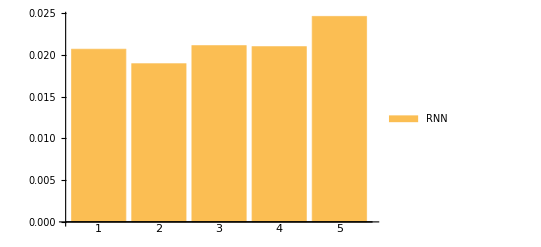

```mathematica
BarChart[{0.02066730778922169,0.018936139793824656,0.02110177576283456,0.020980033292970258,0.02459244698329909},ChartLabels->{1,2,3,4,5}, ChartLegends->{"RNN"}]
```

In the above bar chart, we see that the euclidean distance for all the 5 n-grams are quite close to the actual dataset. In addition, the example that were generated are also plausible examples.

### 2. Company Names

<one-line text, explaining the code only> Plot several functions with a legend:

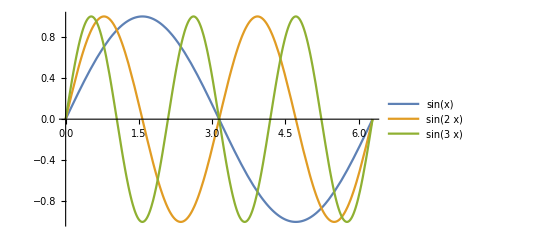

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## 3. GANs for text generation

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

-Graphics-

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...